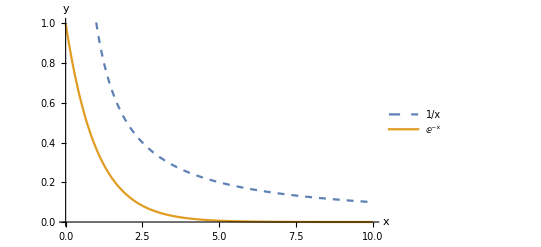

/Users/Rogiel/Documents/GitHub/ufrgs-instrumentacao-lab4/Resources/Mathematica/Images/X1-vs-Exponencial.pdf

```mathematica
comparacao=Plot[{1/x,Exp[-x]}, {x, 0, 10}, PlotLegends->{1/x, Exp[-x]}, PlotStyle->{Dashed, Thick}, AxesLabel->{"x", "y"}]
Export[NotebookDirectory[]<>"Images/X1-vs-Exponencial.pdf", comparacao]
```

```mathematica
data={{16,3340},{16,3330},{18,3000},{18,3000},{20,2810},{20,2770},{22,2590},{22,2530},{24,2380},{24,2400},{26,2180},{26,2160},{28,1990},{28,1970},{30,1790},{30,1770},{32,1650},{32,1640},{34,1540},{34,1520},{36,1360},{36,1380},{38,1310},{38,1300},{40,1210},{40,1180},{42,1110},{42,1090},{44,1020},{44,990},{46,950},{46,930},{48,860},{48,880},{50,810},{50,790},{52,740},{52,740},{54,690},{54,680},{56,630},{56,630},{58,580},{58,580},{60,560},{60,550},{62,520},{62,510},{64,470},{64,480},{66,460},{66,440},{68,420},{68,420},{70,380},{70,380},{72,360},{72,360},{74,340},{74,330}};
data[[All, 1]]=data[[All, 1]]+273;
fitted=NonlinearModelFit[data, R0*Exp[β*(1/T)], {R0, β}, T]
```

FittedModel[0.00430432 ⅇ^(3920.77/T)]

((-R1 R3+R1/(1/RL+1/(Rs+RT))) Vs)/((R2+R3) (R1+1/(1/RL+1/(Rs+RT))))

FittedModel[127.054-4.01143 T]

{-4.14857,-3.02571,-0.702857,0.32,1.14286,3.86571,3.08857,3.41143,1.33429,1.65714,1.68,-2.69714,-1.47429,-4.45143}

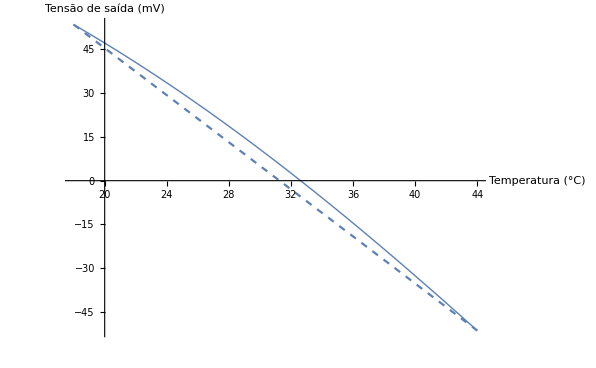

/Users/Rogiel/Documents/GitHub/ufrgs-instrumentacao-lab4/Resources/Mathematica/Images/NTC-Linear-Esperado.pdf

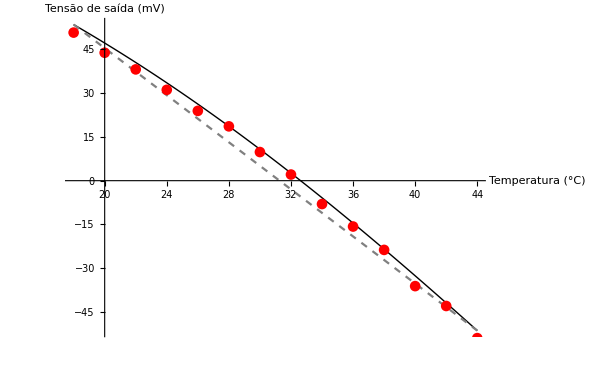

/Users/Rogiel/Documents/GitHub/ufrgs-instrumentacao-lab4/Resources/Mathematica/Images/NTC-Linear-Obtido.pdf

18 | 53.4488
20 | 47.1248
22 | 40.4763
24 | 33.507
26 | 26.2232
28 | 18.6333
30 | 10.7481
32 | 2.58107
34 | -5.85242
36 | -14.5346
38 | -23.4457
40 | -32.5642
42 | -41.8668
44 | -51.3289

```mathematica
linear=Vs*(R1*Rs-R3*R1)/((R2+R3)*(R1+Rs))/.{Rs->1/(1/RL+1/(RT+Rs))}

linearizado=linear/.{R1->530, R2->530, R3->423, RL->550, Rs->227, RT->fitted[T+273], Vs->2000};


medido={{18,50.7},{20,43.8},{22,38.1},{24,31.1},{26,23.9},{28,18.6},{30,9.8},{32,2.1},{34,-8},{36,-15.7},{38,-23.7},{40,-36.1},{42,-42.9},{44,-53.9}};

model=LinearModelFit[medido, T, T]
model["FitResiduals"]

idealLinearModel=LinearModelFit[{{18, linearizado/.{T->18}}, {44, linearizado/.{T->44}}}, x, x];

esperado=Show[
Plot[linearizado, {T, 18, 44}, PlotStyle->Thick],
Plot[idealLinearModel[T], {T, 18, 44}, PlotStyle->Dashed],
AxesLabel->{"Temperatura (°C)", "Tensão de saída (mV)"}
]
Export[NotebookDirectory[]<>"Images/NTC-Linear-Esperado.pdf", esperado]

obtido=Show[
Plot[linearizado, {T, 18, 44}, PlotStyle->{Thick, Black}],
Plot[idealLinearModel[T], {T, 18, 44}, PlotStyle->{Dashed, Gray}],
ListPlot[medido, PlotStyle->Red],
AxesLabel->{"Temperatura (°C)", "Tensão de saída (mV)"}
]
Export[NotebookDirectory[]<>"Images/NTC-Linear-Obtido.pdf", obtido]

Grid[Table[{T, linearizado/.{T->T}},{T, 18, 44, 2}]]
```

```mathematica
Export[NotebookFileName[EvaluationNotebook[]]<>".pdf", EvaluationNotebook[]];
```